## Set your path to NonLinearSolver and get it

```mathematica
dddRicardo="/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m";
```

```mathematica
Get[dddRicardo]
```

### DataToEquations and the critical congestion solver

```mathematica
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{7,U1},{8,U2},{9,U3}},"Switching Costs"->{{5,6,7,1},{5,6,8,1},{5,6,9,1},{7,6,5,1},{7,6,8,1},{7,6,9,1},{8,6,5,1},{8,6,7,1},{8,6,9,1},{9,6,5,1},{9,6,7,1},{9,6,8,1}}|>;
crit=CriticalCongestionSolver[d2e = Data2Equations[Data/.{I1->200,I2->200,U1->0,U2->0, U3->0}]];//AbsoluteTiming
```

{0.111548,Null}

Don’t worry about the last 3 printed terms when checking for the critical congestion case.

```mathematica
IsNonLinearSolution[crit]@crit["AssoCritical"]
```

EqEntryIn: j24==200&&j26==200	True

EqValueAuxiliaryEdges: u23==u24&&u25==u26&&u17==u18&&u19==u20&&u21==u22	True

EqCompCon: (jt1==0||1000000-u1+u24==0)&&(jt2==0||u1-u24==0)&&(jt3==0||1000000+u26-u3==0)&&(jt4==0||-u26+u3==0)&&(jt5==0||-u2+u4==0)&&(jt6==0||-u2+u5==0)&&(jt7==0||u2-u4==0)&&(jt8==0||-u4+u5==0)&&(jt9==0||u2-u5==0)&&(jt10==0||u4-u5==0)&&(jt11==0||-u6+u7==0)&&(jt12==0||u6-u7==0)&&(jt13==0||-u8+u9==0)&&(jt14==0||u8-u9==0)&&(jt15==0||1-u10+u11==0)&&(jt16==0||1-u10+u13==0)&&(jt17==0||1-u10+u15==0)&&(jt18==0||1+u10-u11==0)&&(jt19==0||1-u11+u13==0)&&(jt20==0||1-u11+u15==0)&&(jt21==0||1+u10-u13==0)&&(jt22==0||1+u11-u13==0)&&(jt23==0||1-u13+u15==0)&&(jt24==0||1+u10-u15==0)&&(jt25==0||1+u11-u15==0)&&(jt26==0||1+u13-u15==0)&&(jt27==0||-u12+u17==0)&&(jt28==0||1000000+u12-u17==0)&&(jt29==0||-u14+u19==0)&&(jt30==0||1000000+u14-u19==0)&&(jt31==0||-u16+u21==0)&&(jt32==0||1000000+u16-u21==0)	True

EqBalanceSplittingCurrents: j1==jt1&&j24==jt2&&j3==jt3&&j26==jt4&&j2==jt5+jt6&&j4==jt7+jt8&&j5==jt10+jt9&&j6==jt11&&j7==jt12&&j8==jt13&&j9==jt14&&j10==jt15+jt16+jt17&&j11==jt18+jt19+jt20&&j13==jt21+jt22+jt23&&j15==jt24+jt25+jt26&&j12==jt27&&j17==jt28&&j14==jt29&&j19==jt30&&j16==jt31&&j21==jt32	True

EqCurrentCompCon: (j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0)	True

EqTransitionCompCon: (jt1==0||jt2==0)&&(jt10==0||jt8==0)&&(jt11==0||jt12==0)&&(jt13==0||jt14==0)&&(jt15==0||jt18==0)&&(jt16==0||jt21==0)&&(jt17==0||jt24==0)&&(jt19==0||jt22==0)&&(jt20==0||jt25==0)&&(jt23==0||jt26==0)&&(jt27==0||jt28==0)&&(jt29==0||jt30==0)&&(jt3==0||jt4==0)&&(jt31==0||jt32==0)&&(jt5==0||jt7==0)&&(jt6==0||jt9==0)	True

EqPosJs: j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0	True

EqPosJts: jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt25≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0	True

EqSwitchingByVertex: u1≤1000000+u24&&u24≤u1&&u3≤1000000+u26&&u26≤u3&&u2≤u4&&u2≤u5&&u4≤u2&&u4≤u5&&u5≤u2&&u5≤u4&&u6≤u7&&u7≤u6&&u8≤u9&&u9≤u8&&u10≤1+u11&&u10≤1+u13&&u10≤1+u15&&u11≤1+u10&&u11≤1+u13&&u11≤1+u15&&u13≤1+u10&&u13≤1+u11&&u13≤1+u15&&u15≤1+u10&&u15≤1+u11&&u15≤1+u13&&u12≤u17&&u17≤1000000+u12&&u14≤u19&&u19≤1000000+u14&&u16≤u21&&u21≤1000000+u16	True

Nlhs: {-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16}	{0.,0.,0.,0.,0.,0.,0.,0.}

Nrhs: {-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,4->5],j10-j9-IntM[j10-j9,5->6],-j11+j12-IntM[-j11+j12,6->7],-j13+j14-IntM[-j13+j14,6->8],-j15+j16-IntM[-j15+j16,6->9]}	{-401.066,-401.066,-1002.32,-1002.32,-1002.32,-232.851,-232.851,-232.851}

Max error for non-linear solution: 1002.32

<|j24→200,j26→200,j23→0,j25→0,j17→0,j19→0,j21→0,j2→200,j4→200,j1→0,j3→0,j6→400,j5→0,j8→400,j7→0,j10→400,j9→0,j12→400/3,j14→400/3,j16→400/3,j11→0,j18→400/3,j13→0,j20→400/3,j15→0,j22→400/3,u18→0,u20→0,u22→0,jt11→400,jt12→0,jt17→400/3,jt2→200,jt20→0,jt21→0,jt23→0,jt26→0,jt27→400/3,jt28→0,jt29→400/3,jt3→0,jt30→0,jt31→400/3,jt32→0,jt4→200,jt5→0,jt6→200,jt7→0,jt8→200,jt9→0,u17→0,u19→0,u21→0,u24→4603/3,u26→4603/3,jt1→0,jt10→0,jt13→400,jt14→0,jt18→0,jt19→0,jt22→0,jt24→0,jt25→0,u2→4003/3,u23→4603/3,u3→4603/3,u5→4003/3,u7→2803/3,u9→1603/3,u1→4603/3,u12→0,u14→0,u16→0,u25→4603/3,u4→4003/3,u6→2803/3,u8→1603/3,jt15→400/3,jt16→400/3,u10→403/3,u11→400/3,u13→400/3,u15→400/3|>

#### Non-critical congestion solver

#### Starting from the critical congestion solution

```mathematica
nn=NonLinear[crit];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]];
```

True

<|j24→200,j26→200,j23→0,j25→0,j17→0,j19→0,j21→0,j2→200,j4→200,j1→0,j3→0,j6→400,j5→0,j8→400,j7→0,j10→400,j9→0,j12→400/3,j14→400/3,j16→400/3,j11→0,j18→400/3,j13→0,j20→400/3,j15→0,j22→400/3,u18→0,u20→0,u22→0,jt11→400,jt12→0,jt17→400/3,jt2→200,jt20→0,jt21→0,jt23→0,jt26→0,jt27→400/3,jt28→0,jt29→400/3,jt3→0,jt30→0,jt31→400/3,jt32→0,jt4→200,jt5→0,jt6→200,jt7→0,jt8→200,jt9→0,u17→0,u19→0,u21→0,u24→4603/3,u26→4603/3,jt1→0,jt10→0,jt13→400,jt14→0,jt18→0,jt19→0,jt22→0,jt24→0,jt25→0,u2→4003/3,u23→4603/3,u3→4603/3,u5→4003/3,u7→2803/3,u9→1603/3,u1→4603/3,u12→0,u14→0,u16→0,u25→4603/3,u4→4003/3,u6→2803/3,u8→1603/3,jt15→400/3,jt16→400/3,u10→403/3,u11→400/3,u13→400/3,u15→400/3|>

Iterated 2 times out of 50

{0.163663,Null}

EqEntryIn: j24==200&&j26==200	True

EqValueAuxiliaryEdges: u23==u24&&u25==u26&&u17==u18&&u19==u20&&u21==u22	True

EqCompCon: (jt1==0||1000000-u1+u24==0)&&(jt2==0||u1-u24==0)&&(jt3==0||1000000+u26-u3==0)&&(jt4==0||-u26+u3==0)&&(jt5==0||-u2+u4==0)&&(jt6==0||-u2+u5==0)&&(jt7==0||u2-u4==0)&&(jt8==0||-u4+u5==0)&&(jt9==0||u2-u5==0)&&(jt10==0||u4-u5==0)&&(jt11==0||-u6+u7==0)&&(jt12==0||u6-u7==0)&&(jt13==0||-u8+u9==0)&&(jt14==0||u8-u9==0)&&(jt15==0||1-u10+u11==0)&&(jt16==0||1-u10+u13==0)&&(jt17==0||1-u10+u15==0)&&(jt18==0||1+u10-u11==0)&&(jt19==0||1-u11+u13==0)&&(jt20==0||1-u11+u15==0)&&(jt21==0||1+u10-u13==0)&&(jt22==0||1+u11-u13==0)&&(jt23==0||1-u13+u15==0)&&(jt24==0||1+u10-u15==0)&&(jt25==0||1+u11-u15==0)&&(jt26==0||1+u13-u15==0)&&(jt27==0||-u12+u17==0)&&(jt28==0||1000000+u12-u17==0)&&(jt29==0||-u14+u19==0)&&(jt30==0||1000000+u14-u19==0)&&(jt31==0||-u16+u21==0)&&(jt32==0||1000000+u16-u21==0)	True

EqBalanceSplittingCurrents: j1==jt1&&j24==jt2&&j3==jt3&&j26==jt4&&j2==jt5+jt6&&j4==jt7+jt8&&j5==jt10+jt9&&j6==jt11&&j7==jt12&&j8==jt13&&j9==jt14&&j10==jt15+jt16+jt17&&j11==jt18+jt19+jt20&&j13==jt21+jt22+jt23&&j15==jt24+jt25+jt26&&j12==jt27&&j17==jt28&&j14==jt29&&j19==jt30&&j16==jt31&&j21==jt32	True

EqCurrentCompCon: (j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0)	True

EqTransitionCompCon: (jt1==0||jt2==0)&&(jt10==0||jt8==0)&&(jt11==0||jt12==0)&&(jt13==0||jt14==0)&&(jt15==0||jt18==0)&&(jt16==0||jt21==0)&&(jt17==0||jt24==0)&&(jt19==0||jt22==0)&&(jt20==0||jt25==0)&&(jt23==0||jt26==0)&&(jt27==0||jt28==0)&&(jt29==0||jt30==0)&&(jt3==0||jt4==0)&&(jt31==0||jt32==0)&&(jt5==0||jt7==0)&&(jt6==0||jt9==0)	True

EqPosJs: j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0	True

EqPosJts: jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt25≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0	True

EqSwitchingByVertex: u1≤1000000+u24&&u24≤u1&&u3≤1000000+u26&&u26≤u3&&u2≤u4&&u2≤u5&&u4≤u2&&u4≤u5&&u5≤u2&&u5≤u4&&u6≤u7&&u7≤u6&&u8≤u9&&u9≤u8&&u10≤1+u11&&u10≤1+u13&&u10≤1+u15&&u11≤1+u10&&u11≤1+u13&&u11≤1+u15&&u13≤1+u10&&u13≤1+u11&&u13≤1+u15&&u15≤1+u10&&u15≤1+u11&&u15≤1+u13&&u12≤u17&&u17≤1000000+u12&&u14≤u19&&u19≤1000000+u14&&u16≤u21&&u21≤1000000+u16	True

Nlhs: {-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16}	{-401.066,-401.066,-1002.32,-1002.32,-1002.32,-232.851,-232.851,-232.851}

Nrhs: {-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,4->5],j10-j9-IntM[j10-j9,5->6],-j11+j12-IntM[-j11+j12,6->7],-j13+j14-IntM[-j13+j14,6->8],-j15+j16-IntM[-j15+j16,6->9]}	{-401.066,-401.066,-1002.32,-1002.32,-1002.32,-232.851,-232.851,-232.851}

Max error for non-linear solution: 2.21689×10^-12

#### Starting from the zero cpc’s

```mathematica
Get[dddRicardo]
nn=NonLinear[d2e];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]];
```

True

<|j24→200,j26→200,j23→0,j25→0,j17→0,j19→0,j21→0,j2→200,j4→200,j1→0,j3→0,j6→400,j5→0,j8→400,j7→0,j10→400,j9→0,j12→400/3,j14→400/3,j16→400/3,j11→0,j18→400/3,j13→0,j20→400/3,j15→0,j22→400/3,u18→0,u20→0,u22→0,jt11→400,jt12→0,jt17→400/3,jt2→200,jt20→0,jt21→0,jt23→0,jt26→0,jt27→400/3,jt28→0,jt29→400/3,jt3→0,jt30→0,jt31→400/3,jt32→0,jt4→200,jt5→0,jt6→200,jt7→0,jt8→200,jt9→0,u17→0,u19→0,u21→0,u24→4603/3,u26→4603/3,jt1→0,jt10→0,jt13→400,jt14→0,jt18→0,jt19→0,jt22→0,jt24→0,jt25→0,u2→4003/3,u23→4603/3,u3→4603/3,u5→4003/3,u7→2803/3,u9→1603/3,u1→4603/3,u12→0,u14→0,u16→0,u25→4603/3,u4→4003/3,u6→2803/3,u8→1603/3,jt15→400/3,jt16→400/3,u10→403/3,u11→400/3,u13→400/3,u15→400/3|>

Iterated 2 times out of 50

{0.178953,Null}

EqEntryIn: j24==200&&j26==200	True

EqValueAuxiliaryEdges: u23==u24&&u25==u26&&u17==u18&&u19==u20&&u21==u22	True

EqCompCon: (jt1==0||1000000-u1+u24==0)&&(jt2==0||u1-u24==0)&&(jt3==0||1000000+u26-u3==0)&&(jt4==0||-u26+u3==0)&&(jt5==0||-u2+u4==0)&&(jt6==0||-u2+u5==0)&&(jt7==0||u2-u4==0)&&(jt8==0||-u4+u5==0)&&(jt9==0||u2-u5==0)&&(jt10==0||u4-u5==0)&&(jt11==0||-u6+u7==0)&&(jt12==0||u6-u7==0)&&(jt13==0||-u8+u9==0)&&(jt14==0||u8-u9==0)&&(jt15==0||1-u10+u11==0)&&(jt16==0||1-u10+u13==0)&&(jt17==0||1-u10+u15==0)&&(jt18==0||1+u10-u11==0)&&(jt19==0||1-u11+u13==0)&&(jt20==0||1-u11+u15==0)&&(jt21==0||1+u10-u13==0)&&(jt22==0||1+u11-u13==0)&&(jt23==0||1-u13+u15==0)&&(jt24==0||1+u10-u15==0)&&(jt25==0||1+u11-u15==0)&&(jt26==0||1+u13-u15==0)&&(jt27==0||-u12+u17==0)&&(jt28==0||1000000+u12-u17==0)&&(jt29==0||-u14+u19==0)&&(jt30==0||1000000+u14-u19==0)&&(jt31==0||-u16+u21==0)&&(jt32==0||1000000+u16-u21==0)	True

EqBalanceSplittingCurrents: j1==jt1&&j24==jt2&&j3==jt3&&j26==jt4&&j2==jt5+jt6&&j4==jt7+jt8&&j5==jt10+jt9&&j6==jt11&&j7==jt12&&j8==jt13&&j9==jt14&&j10==jt15+jt16+jt17&&j11==jt18+jt19+jt20&&j13==jt21+jt22+jt23&&j15==jt24+jt25+jt26&&j12==jt27&&j17==jt28&&j14==jt29&&j19==jt30&&j16==jt31&&j21==jt32	True

EqCurrentCompCon: (j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0)	True

EqTransitionCompCon: (jt1==0||jt2==0)&&(jt10==0||jt8==0)&&(jt11==0||jt12==0)&&(jt13==0||jt14==0)&&(jt15==0||jt18==0)&&(jt16==0||jt21==0)&&(jt17==0||jt24==0)&&(jt19==0||jt22==0)&&(jt20==0||jt25==0)&&(jt23==0||jt26==0)&&(jt27==0||jt28==0)&&(jt29==0||jt30==0)&&(jt3==0||jt4==0)&&(jt31==0||jt32==0)&&(jt5==0||jt7==0)&&(jt6==0||jt9==0)	True

EqPosJs: j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0	True

EqPosJts: jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt25≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0	True

EqSwitchingByVertex: u1≤1000000+u24&&u24≤u1&&u3≤1000000+u26&&u26≤u3&&u2≤u4&&u2≤u5&&u4≤u2&&u4≤u5&&u5≤u2&&u5≤u4&&u6≤u7&&u7≤u6&&u8≤u9&&u9≤u8&&u10≤1+u11&&u10≤1+u13&&u10≤1+u15&&u11≤1+u10&&u11≤1+u13&&u11≤1+u15&&u13≤1+u10&&u13≤1+u11&&u13≤1+u15&&u15≤1+u10&&u15≤1+u11&&u15≤1+u13&&u12≤u17&&u17≤1000000+u12&&u14≤u19&&u19≤1000000+u14&&u16≤u21&&u21≤1000000+u16	True

Nlhs: {-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16}	{-401.066,-401.066,-1002.32,-1002.32,-1002.32,-232.851,-232.851,-232.851}

Nrhs: {-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,4->5],j10-j9-IntM[j10-j9,5->6],-j11+j12-IntM[-j11+j12,6->7],-j13+j14-IntM[-j13+j14,6->8],-j15+j16-IntM[-j15+j16,6->9]}	{-401.066,-401.066,-1002.32,-1002.32,-1002.32,-232.851,-232.851,-232.851}

Max error for non-linear solution: 2.21689×10^-12

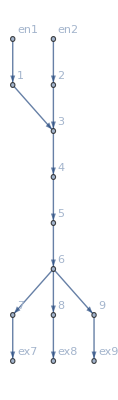

```mathematica
d2e["FG"]
```